```mathematica
tstart=AbsoluteTime[];
nproc=1;
LaunchKernels[nproc];
SetDirectory[NotebookDirectory[]];
```

```mathematica
ℏ=1;
```

```mathematica
discHeff=Import["H.mat"];
discHeff=discHeff[[1]];
```

```mathematica
ψ0=Import["psi0.mat"];
ψ0=Transpose[ψ0[[1]]][[1]];
```

```mathematica
tfinal=30000;
τ=1;
trange=Range[0,tfinal,τ];
```

```mathematica
Heff=Interpolation[Thread[{trange,discHeff}]];
```

```mathematica
test[t_]:=Heff[t]-Transpose[Heff[t]];
```

```mathematica
true=First[Evaluate[ψ/.NDSolve[{I ℏ ψ'[t]==Heff[t].ψ[t],ψ[0]==ψ0},ψ,{t,0,tfinal}]]];
```

```mathematica
td=Table[true[t],{t,0,tfinal,τ}];
```

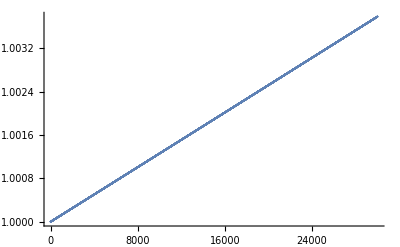

```mathematica
ListPlot[Table[Conjugate[td[[i]]].td[[i]],{i,1,tfinal/τ}]]
```

```mathematica
Export["td.mat",td];
Print["TDSE state exported."]
tend=AbsoluteTime[];
ttotal=tend-tstart;
Print[" Total time: ",ttotal];
```

TDSE state exported.

Total time: 211.85219